```mathematica
ClearAll["Global`*"]
```

```mathematica
GBM[P_,t_]:=GeometricBrownianMotionProcess[μ,σ,P][t]
```

```mathematica
Mean[GBM[P,t]]//FullSimplify
```

ⅇ^(t μ) P

```mathematica
ℭ[x_,P_,t_]:=FullSimplify[CDF[GBM[P,t],x],{x>0,t>0}]
```

```mathematica
ℭ[x,P,t]//FullSimplify
```

```mathematica
1/2 Erfc[(t μ-(t σ^2)/2+Log[P]-Log[x])/(√2 √t σ)]-1/2 Erfc[(t( μ-σ^2/2)+Log[P/x])/(√(2 t) σ)]//PowerExpand//FullSimplify
```

0

```mathematica
FullSimplify[Probability[p<x,p\[Distributed]GeometricBrownianMotionProcess[μ,σ,P][t]],x>0]
```

```mathematica
𝔓[x_,P_,t_]:=FullSimplify[PDF[GBM[P,t]][x],x>0]
```

```mathematica
𝔓[x,P,t]//FullSimplify
```

```mathematica
(ⅇ^(-((t (-2 μ+σ^2)-2 Log[P]+2 Log[x])^2)/(8 t σ^2)))/(√(2 π) √t x σ)-(ⅇ^(-(( t ( μ-σ^2/2)+Log[P/x])^2)/(2 t σ^2)))/(√(2 π t) x σ)//PowerExpand//FullSimplify
```

0

```mathematica
t (-2 μ+σ^2)-2 Log[P]+2 Log[x]-(Log[x/P]-t ( μ-σ^2/2))*2//PowerExpand//FullSimplify
```

0

```mathematica
Log[P]-Log[x]+Log[x/P]
```

Log[P]-Log[x]+Log[x/P]

```mathematica
𝔘[P_,T_,S_,A_]:=((1+α[A]*S)*P)/ⅇ^(r[A]*T)
```

lower bound

```mathematica
P3lo[P0_]:=P0/((1+α[1])*ⅇ^((μ-r[1])*Subscript[τ, b]+r[1]*(Subscript[τ, a]+Subscript[τ, e])))
```

Probability to be lower than lower bound

```mathematica
p[x_,P0_]:=ℭ[P3lo[P0],x,Subscript[τ, b]]
```

```mathematica
p[x,P0]//FullSimplify
```

1/2 Erfc[(2 Log[(ⅇ^((μ-r[1]) τ_b+r[1] (τ_a+τ_e)) x (1+α[1]))/P0]+(2 μ-σ^2) τ_b)/(2 √2 σ √τ_b)]

```mathematica
𝔘Bc[x_,P0_]:=(1-p[x,P0])*𝔘[P0,Subscript[τ, a]+Subscript[τ, e],1,2]+p[x,P0]*𝔘[Mean[GBM[x,2*Subscript[τ, b]]],2*Subscript[τ, b],0,2]
```

```mathematica
𝔘Bc[x,P0]//FullSimplify
```

```mathematica
𝔘Bc[x_,P0_]:=1/2 ⅇ^(-r[2] (Subscript[τ, a]+2 Subscript[τ, b]+Subscript[τ, e])) (2 ⅇ^(2 r[2] Subscript[τ, b]) P0 (1+α[2])-Erfc[(2 Log[(ⅇ^((μ-r[1]) Subscript[τ, b]+r[1] (Subscript[τ, a]+Subscript[τ, e])) x (1+α[1]))/P0]+(2 μ-σ^2) Subscript[τ, b])/(2 √2 σ √Subscript[τ, b])] (-ⅇ^(2 μ Subscript[τ, b]+r[2] (Subscript[τ, a]+Subscript[τ, e])) x+ⅇ^(2 r[2] Subscript[τ, b]) P0 (1+α[2])))
∫_P3lo[P0]^∞ 𝔓[P3,P2,Subscript[τ, b]]*𝔘[Mean[GBM[P3,Subscript[τ, b]]],Subscript[τ, b],1,1]ⅆP3//FullSimplify
```

ConditionalExpression[1/2 ⅇ^((2 μ-r[1]) τ_b) P2 (Erf[(2 (Log[P2]-Log[(ⅇ^(-μ τ_b-r[1] (τ_a-τ_b+τ_e)) P0)/(1+α[1])])+(2 μ+σ^2) τ_b)/(2 √2 σ √τ_b)]+σ √(1/(σ^2 τ_b)) √τ_b) (1+α[1]),(ⅇ^(ⅈ Im[(μ-r[1]) τ_b+r[1] (τ_a+τ_e)])+Sign[P0]/Sign[1+α[1]]≠0||(ⅇ^((-μ+r[1]) τ_b-r[1] (τ_a+τ_e)) P0)/(1+α[1])∉ℝ)&&((Re[1/(σ^2 τ_b)]==0&&Re[(Log[P2]+μ τ_b)/(σ^2 τ_b)]<-1/2)||Re[1/(σ^2 τ_b)]>0)]

```mathematica
𝔘Bc[x,P0]-x//FullSimplify
```

-x+1/2 ⅇ^(-r[2] (τ_a+2 τ_b+τ_e)) (2 ⅇ^(2 r[2] τ_b) P0 (1+α[2])-Erfc[(2 Log[(ⅇ^((μ-r[1]) τ_b+r[1] (τ_a+τ_e)) x (1+α[1]))/P0]+(2 μ-σ^2) τ_b)/(2 √2 σ √τ_b)] (-ⅇ^(2 μ τ_b+r[2] (τ_a+τ_e)) x+ⅇ^(2 r[2] τ_b) P0 (1+α[2])))

```mathematica
α[1]=3
α[2]=4
```

3

4

```mathematica
𝔘[P,T,S,2]
```

ⅇ^(-T r[2]) P (1+4 S)

```mathematica
μ=0.002
σ=1
```

0.002

1

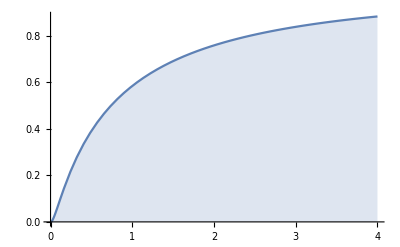

```mathematica
Plot[ℭ[x,2,2],{x,0,4},Filling->Axis]
```

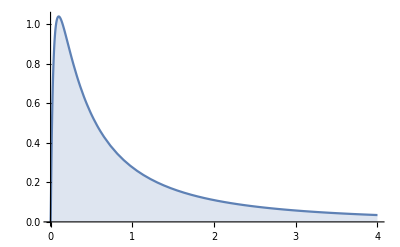

```mathematica
Plot[𝔓[x,2,2],{x,0,4},Filling->Axis]
```

```mathematica
U[P_,T_,Ds_,Dc_,β_:Subscript[β, A],γ_:Subscript[γ, A],δ_:Subscript[δ, A]]:=((1+γ*Ds+δ*Ds*Dc)*P)/ⅇ^(β*T)
```

(ⅇ^(-((2 Log[x]-2 Log[P_t_3]+(-2 μ+σ^2) τ_b)^2)/(8 σ^2 τ_b)))/(√(2 π) x σ √τ_b)

```mathematica
P4A1=Mean[GBM[Subscript[P, Subscript[t, 3]],μ,σ,Subscript[τ, b]]]*(1-2*Subscript[ϵ, 2])//FullSimplify
```

ⅇ^(μ τ_b) P_t_3 (1-2 ϵ_2)

```mathematica
U4A1=U[P4A1,Subscript[τ, b],1,1]//FullSimplify
```

ⅇ^((μ-β_A) τ_b) P_t_3 (1+γ_A+δ_A) (1-2 ϵ_2)

```mathematica
U4A2=U[Subscript[P, 0]-2*Subscript[ϵ, 1],Subscript[τ, ϵ]+Subscript[τ, a],0,0]//FullSimplify
```

ⅇ^(-β_A (τ_a+τ_ϵ)) (P_0-2 ϵ_1)

```mathematica
Collect[U4A1>U4A2//FullSimplify,Subscript[P, Subscript[t, 3]]]//FullSimplify
```

ⅇ^((μ-β_A) τ_b) P_t_3 (1+γ_A+δ_A) (1-2 ϵ_2)>ⅇ^(-β_A (τ_a+τ_ϵ)) (P_0-2 ϵ_1)

```mathematica
Solve[ⅇ^((μ-Subscript[β, A]) Subscript[τ, b]) Subscript[P, Subscript[t, 3]] (1+Subscript[γ, A]+Subscript[δ, A]) (1-2 Subscript[ϵ, 2])==ⅇ^(-Subscript[β, A] (Subscript[τ, a]+Subscript[τ, ϵ])) (Subscript[P, 0]-2 Subscript[ϵ, 1]),Subscript[P, Subscript[t, 3]]]
```

{{P_t_3→-(ⅇ^(-(μ-β_A) τ_b-β_A (τ_a+τ_ϵ)) (P_0-2 ϵ_1))/((1+γ_A+δ_A) (-1+2 ϵ_2))}}

```mathematica
-(ⅇ^(-(μ-Subscript[β, A]) Subscript[τ, b]-Subscript[β, A] (Subscript[τ, a]+Subscript[τ, ϵ])) (Subscript[P, 0]-2 Subscript[ϵ, 1]))/((1+Subscript[γ, A]+Subscript[δ, A]) (-1+2 Subscript[ϵ, 2]))-(Subscript[P, 0]-2 Subscript[ϵ, 1])/((1+Subscript[γ, A]+Subscript[δ, A]) (1-2 Subscript[ϵ, 2])*ⅇ^((μ-Subscript[β, A]) Subscript[τ, b]+Subscript[β, A] (Subscript[τ, a]+Subscript[τ, ϵ])))//FullSimplify
```

0

```mathematica
FullSimplify[PDF[GBM[Subscript[P, Subscript[t, 2]],μ,σ,Subscript[τ, b]]][x],x>0]
```

```mathematica
(ⅇ^(-((2 Log[x]-2 Log[Subscript[P, Subscript[t, 2]]]+(-2 μ+σ^2) Subscript[τ, b])^2)/(8 σ^2 Subscript[τ, b])))/(√(2 π) x σ √Subscript[τ, b])//FullSimplify
```

```mathematica
FullSimplify[CDF[GBM[Subscript[P, Subscript[t, 2]],μ,σ,Subscript[τ, b]]][x],x>0]
```

1/2 Erfc[(Log[P_t_2/x]+(μ-σ^2/2) τ_b)/(√2 σ √τ_b)]

```mathematica
Temp[x_]:=FullSimplify[Probability[Subscript[P, Subscript[t, 3]]>x,Subscript[P, Subscript[t, 3]]\[Distributed]GBM[Subscript[P, Subscript[t, 2]],μ,σ,Subscript[τ, b]]],x>0]
```

```mathematica
Temp[x]
```

1/2 (1+Erf[(Log[P_t_2/x]+(μ-σ^2/2) τ_b)/(√2 σ √τ_b)])

```mathematica
Temp[(Subscript[P, 0]-2 Subscript[ϵ, 1])/((1+Subscript[γ, A]+Subscript[δ, A]) (1-2 Subscript[ϵ, 2])*ⅇ^((μ-Subscript[β, A]) Subscript[τ, b]+Subscript[β, A] (Subscript[τ, a]+Subscript[τ, ϵ])))]
```

```mathematica
p=1/2 (1+Erf[(Log[Subscript[P, Subscript[t, 2]]]-Log[-(ⅇ^((-μ+Subscript[β, A]) Subscript[τ, b]-Subscript[β, A] (Subscript[τ, a]+Subscript[τ, ϵ])) Subscript[α, A] (Subscript[P, 0]-2 Subscript[ϵ, 1]))/((Subscript[α, A]+Subscript[γ, A]+Subscript[δ, A]) (-1+2 Subscript[ϵ, 2]))]+(μ-σ^2/2) Subscript[τ, b])/(√2 σ √Subscript[τ, b])])//FullSimplify
```

1/2 (1+Erf[(Log[P_t_2]-Log[-(ⅇ^((-μ+β_A) τ_b-β_A (τ_a+τ_ϵ)) α_A (P_0-2 ϵ_1))/((α_A+γ_A+δ_A) (-1+2 ϵ_2))]+(μ-σ^2/2) τ_b)/(√2 σ √τ_b)])

```mathematica
P3A=Mean[GBM[Subscript[P, Subscript[t, 2]],μ,σ,2*Subscript[τ, b]]]*(1-2*Subscript[ϵ, 2])//FullSimplify
```

ⅇ^(2 μ τ_b) P_t_2 (1-2 ϵ_2)

```mathematica
U3B1=p*U[Subscript[P, 0]-2*Subscript[ϵ, 1],Subscript[τ, ϵ]+Subscript[τ, α],1,1,Subscript[β, B],Subscript[γ, B],Subscript[δ, B]]+(1-p)*U[P3A,2*Subscript[τ, b],1,0,Subscript[β, B],Subscript[γ, B],Subscript[δ, B]]//FullSimplify
```

ⅇ^(-β_B (τ_α+τ_ϵ)) p (α_B+γ_B+δ_B) (P_0-2 ϵ_1)+ⅇ^(2 (μ-β_B) τ_b) (-1+p) P_t_2 (α_B+γ_B) (-1+2 ϵ_2)

```mathematica
U3B2=α*Subscript[P, Subscript[t, 2]]
```

α P_t_2

```mathematica
U3B1>U3B2\\FullSimplify
```

```mathematica
U3B1>U3B2
```

```mathematica
Solve[1/2 (ⅇ^(-β (Subscript[τ, α]+Subscript[τ, ϵ])) (α+γ+δ) (1+Erf[(Log[Subscript[P, Subscript[t, 2]]]-Log[-(ⅇ^((β-μ) Subscript[τ, b]-β (Subscript[τ, a]+Subscript[τ, ϵ])) α (Subscript[P, 0]-2 Subscript[ϵ, 1]))/((α+γ+δ) (-1+2 Subscript[ϵ, 2]))]+(μ-σ^2/2) Subscript[τ, b])/(√2 σ √Subscript[τ, b])]) (Subscript[P, 0]-2 Subscript[ϵ, 1])-ⅇ^(2 (-β+μ) Subscript[τ, b]) (α+γ) Erfc[(Log[Subscript[P, Subscript[t, 2]]]-Log[-(ⅇ^((β-μ) Subscript[τ, b]-β (Subscript[τ, a]+Subscript[τ, ϵ])) α (Subscript[P, 0]-2 Subscript[ϵ, 1]))/((α+γ+δ) (-1+2 Subscript[ϵ, 2]))]+(μ-σ^2/2) Subscript[τ, b])/(√2 σ √Subscript[τ, b])] Subscript[P, Subscript[t, 2]] (-1+2 Subscript[ϵ, 2]))==α Subscript[P, Subscript[t, 2]],Subscript[P, Subscript[t, 2]]]
```

Solve[1/2 (ⅇ^(-β (τ_α+τ_ϵ)) (α+γ+δ) (1+Erf[(Log[P_t_2]-Log[-(ⅇ^((β-μ) τ_b-β (τ_a+τ_ϵ)) α (P_0-2 ϵ_1))/((α+γ+δ) (-1+2 ϵ_2))]+(μ-σ^2/2) τ_b)/(√2 σ √τ_b)]) (P_0-2 ϵ_1)-ⅇ^(2 (-β+μ) τ_b) (α+γ) Erfc[(Log[P_t_2]-Log[-(ⅇ^((β-μ) τ_b-β (τ_a+τ_ϵ)) α (P_0-2 ϵ_1))/((α+γ+δ) (-1+2 ϵ_2))]+(μ-σ^2/2) τ_b)/(√2 σ √τ_b)] P_t_2 (-1+2 ϵ_2))==α P_t_2,P_t_2]